## Datorövning 2

Examensarbete

ChartLabels→Placed[Center,#1&]

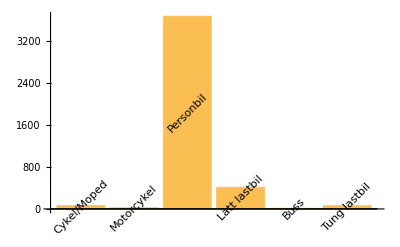

```mathematica
aford={64, 23, 3666,411,11, 63};
afordLabel={"Cykel/Moped", "Motorcykel","Personbil", "Lätt lastbil", "Buss", "Tung lastbil"};
ChartLabels->Placed[Center,Rotate[#,180Degree]&]
BarChart[aford,ChartLabels->Placed[afordLabel, Center, Rotate[#, 45 Degree] &]]
```

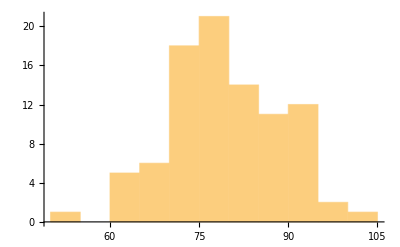

```mathematica
v08={68,71,70,78,92,62,79,71,79,73,87,86,85,85,73,92,100,64,78,85,86,82,72,81,78,73,71,76,92,93,81,94,78,77,82,70,79,63,76,83,82,64,76,71,79,78,71,88,79,72,88,65,81,78,65,71,86,91,81,82,69,90,92,98,79,83,71,52,88,74,68,75,83,91,70,91,84,78,92,83,61,96,75,70,80,91,69,78,79,85,74};
v12={75,64,53,84,94,83,86,70,73,84,88,80,81,65,81,103,59,82,79,67,81,81,72,72,89,96,83,83,68,87,72,56,78,64,82,81,94,81,87,74,83};
v17={97,76,84,57,75,77,78,91,65,78,72,92,73,87,77,67,82,65,75,70,73,85,85,81,83,79,65,80,73,76,69,101,63,71,70,91,95,80,86,77,81,85,75,92,92,77,91,82,83,78,72,77,91,89,62,57,91,73,77,81,66,70,73,75,71,82,87,65,75,73,77,87,83,89,84,69,90,84,80,80,75,102,79,69,71,88,63,65};


Histogram[v08, 10]
```

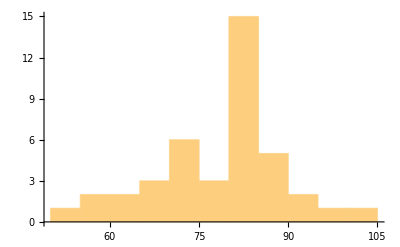

```mathematica
Histogram[v12,10]
```

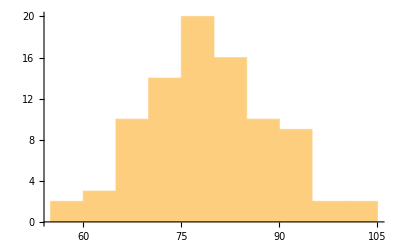

```mathematica
Histogram[v17,10]
```

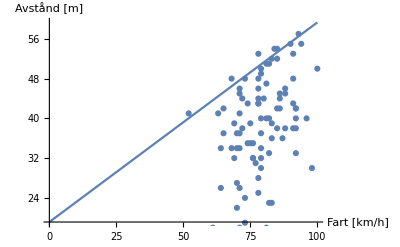

```mathematica
va08={{68,48},{71,34},{70,22},{78,28},{92,38},{62,17},{79,40},{71,37},{79,37},{73,19},{87,36},{86,42},{85,52},{85,42},{73,24},{92,42},{100,50},{64,26},{78,48},{85,54},{86,45},{82,23},{72,38},{81,18},{78,44},{73,48},{71,41},{76,32},{92,33},{93,57},{81,47},{94,55},{78,43},{77,31},{82,40},{70,34},{79,30},{63,41},{76,32},{83,36},{82,51},{64,34},{76,35},{71,46},{79,34},{78,43},{71,18},{88,46},{79,49},{72,44},{88,38},{65,37},{81,51},{78,25},{65,42},{71,45},{86,44},{91,48},{81,40},{82,33},{69,39},{90,55},{92,42},{98,30},{79,32},{83,39},{71,26},{52,41},{88,45},{74,43},{68,34},{75,39},{83,52},{91,53},{70,27},{91,43},{84,54},{78,46},{92,40},{83,23},{61,18},{96,40},{75,35},{70,37},{80,44},{91,38},{69,32},{78,53},{79,50},{85,38},{74,35}};
va12={{75,17},{64,15},{53,29},{84,39},{94,88},{83,22},{86,34},{70,21},{73,60},{84,57},{88,15},{80,8},{81,2},{65,91},{81,5},{103,143},{59,34},{82,44},{79,13},{67,44},{81,46},{81,9},{72,57},{72,10},{89,11},{96,2},{83,7},{83,21},{68,33},{87,12},{72,95},{56,8},{78,6},{64,10},{82,14},{81,6},{94,36},{81,20},{87,7},{74,77},{83,40}};
va17={{97,45},{76,45},{84,45},{57,52},{75,42},{77,52},{78,30},{91,38},{65,20},{78,50},{72,44},{92,46},{73,42},{87,40},{77,56},{67,34},{82,27},{65,33},{75,23},{70,33},{73,40},{85,27},{85,35},{81,29},{83,33},{79,50},{65,61},{80,28},{73,31},{76,37},{69,37},{101,46},{63,35},{71,32},{70,48},{91,45},{95,49},{80,29},{86,28},{77,44},{81,16},{85,45},{75,34},{92,35},{92,59},{77,49},{91,48},{82,40},{83,47},{78,35},{72,54},{77,49},{91,33},{89,51},{62,45},{57,26},{91,43},{73,34},{77,21},{81,49},{66,33},{70,27},{73,16},{75,34},{71,56},{82,48},{87,51},{65,26},{75,41},{73,31},{77,22},{87,45},{83,47},{89,40},{84,41},{69,38},{90,52},{84,27},{80,36},{80,35},{75,35},{102,39},{79,36},{69,24},{71,50},{88,34},{63,31},{65,27}};

p1=ListPlot[va08, AxesLabel->{"Fart [km/h]", "Avstånd [m]"}]
p2=Plot[a1 (t-1900)+b1, {t, 0, 100}, AxesLabel->{"Fart [km/h]", "Avstånd [m]"}]
Show[p2,p1]
```

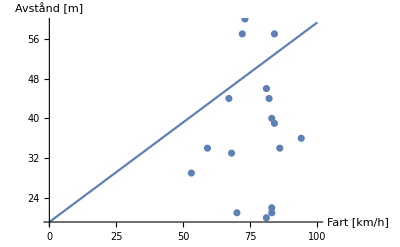

```mathematica
p3=ListPlot[va12, AxesLabel->{"Fart [km/h]", "Avstånd [m]"}]
p4=Plot[a1 (t-1900)+b1, {t, 0, 100}, AxesLabel->{"Fart [km/h]", "Avstånd [m]"}]
Show[p4,p3]
```

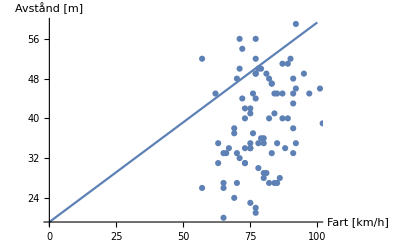

```mathematica
p5=ListPlot[va17, AxesLabel->{"Fart [km/h]", "Avstånd [m]"}]
p6=Plot[a1 (t-1900)+b1, {t, 0, 100}, AxesLabel->{"Fart [km/h]", "Avstånd [m]"}]
Show[p6,p5]
```

Ekvationslösning

```mathematica
Solve[x^4-3 x^3-12 x^2+6x+20==0, x]
```

{{x→-2},{x→5},{x→-√2},{x→√2}}

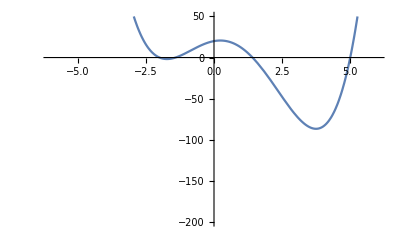

```mathematica
{{x->-2},{x->5},{x->-√2},{x->√2}}

Plot[{x^4-3 x^3-12 x^2+6x+20}, {x, -6,6}, PlotRange->{{-6,6}, {-100,100}}]
```

Expoentional och logaritmer funktioner

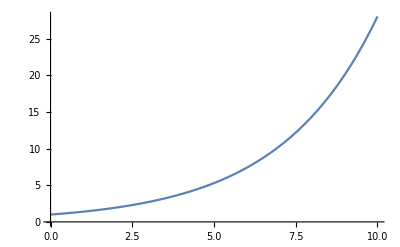

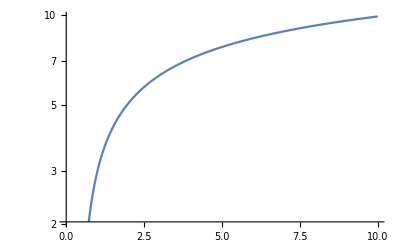

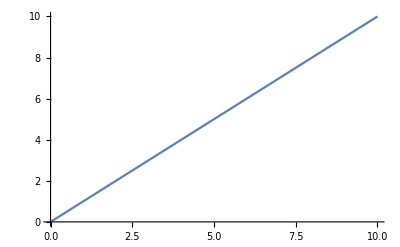

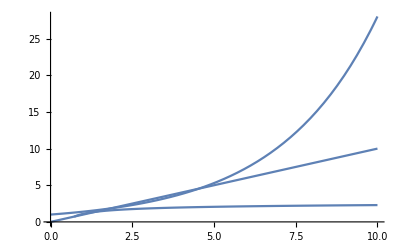

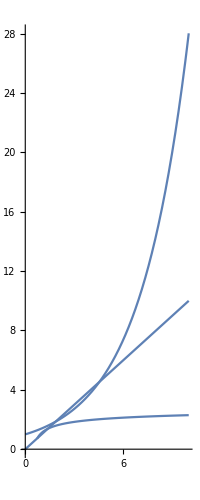

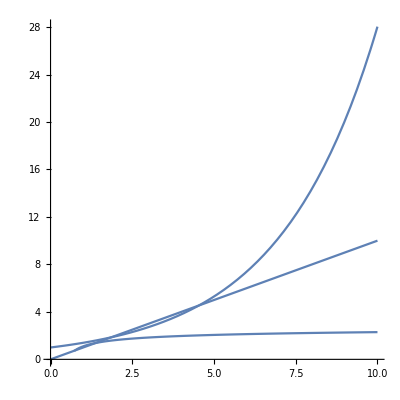

```mathematica
p40 = Plot[ⅇ^(1/3x) ,{x,0,10}] 
p41 = LogPlot[3Log[ⅇ x],{x,0,10} ]
p42 = Plot[x,{x,0,10}]
Show[{p40,p41,p42}]
Show[{p40,p41,p42}, AspectRatio->Automatic]
Show[{p40,p41,p42}, AspectRatio-> 1 ]
```

Radioaktiva isotoper

```mathematica
Uppmät data:
```

```mathematica
data = {(10;21.34),(11;20.6),(12;20.05),(14;18.87),(15;18.30)}
```

{21.34,20.6,20.05,18.87,18.3}

```mathematica
FindFit för att passande graf
```

```mathematica
{a1,b1}={a,b}/.FindFit[data,{a×k^b},{a,b},k]
```

{21.6272,-0.0919245}

```mathematica
Skapar en funktion med hjälp av FindFit
```

```mathematica
f=Function[x,a+b x]/.FindFit[data,a+b x,{a,b},x];
```

```mathematica
Plottar funktionen
```

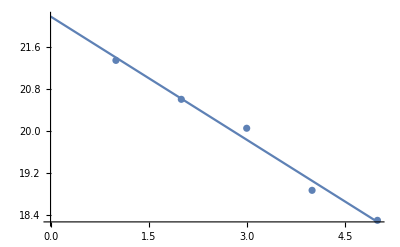

```mathematica
Plot[f[x],{x,0,5}]~Show~ListPlot[data]
```

Som man ser så när x-värdet(tiden från 10 sek ) ökar så minskar den totala massan(M_A och M_B).